

```mathematica
Plot[x,{x,-2,2}]
```

```mathematica
PDF[NormalDistribution[],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
{x,x}.RotationMatrix[π ⅇ^(-x^2/2)]
```

{x Cos[ⅇ^(-x^2/2) π]+x Sin[ⅇ^(-x^2/2) π],x Cos[ⅇ^(-x^2/2) π]-x Sin[ⅇ^(-x^2/2) π]}

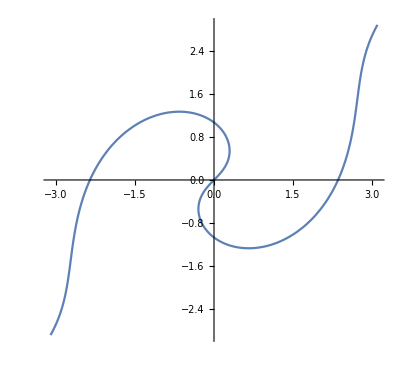

```mathematica
ParametricPlot[
{x Cos[ⅇ^(-x^2/2) π]+x Sin[ⅇ^(-x^2/2) π],x Cos[ⅇ^(-x^2/2) π]-x Sin[ⅇ^(-x^2/2) π]}
,{x,-3,3}]
```

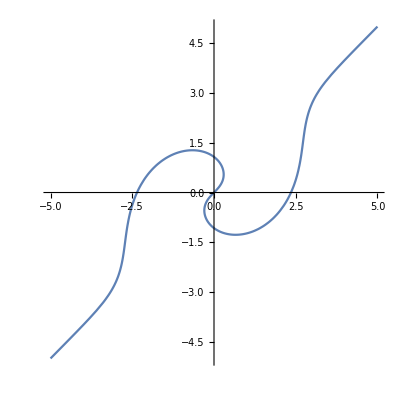

```mathematica
ParametricPlot[
{x Cos[ⅇ^(-x^2/2) π]+x Sin[ⅇ^(-x^2/2) π],x Cos[ⅇ^(-x^2/2) π]-x Sin[ⅇ^(-x^2/2) π]}
,{x,-5,5}]
```

```mathematica
Manipulate[
ParametricPlot[
{x,x}.RotationMatrix[θ ⅇ^(-x^2/2)]
,{x,-5,5}]
,{θ,0,2π}]
```

```mathematica
Manipulate[
ParametricPlot[
{x,x}.RotationMatrix[θ ⅇ^(-x^2/2)]
,{x,-5,5}]
,{θ,0,8π}]
```

```mathematica
Manipulate[
ParametricPlot[
{x,x}.ReflectionMatrix[θ ⅇ^(-x^2/2)]
,{x,-5,5}]
,{θ,0,8π}]
```

ReflectionMatrix::inpv: 0. is not a vector.

General::stop: Further output of ReflectionMatrix::inpv will be suppressed during this calculation.

ReflectionMatrix::inpv: 3.65651×10^-6 is not a vector.

ReflectionMatrix::inpv: 9.93487×10^-6 is not a vector.

ReflectionMatrix::inpv: 0.0000258922 is not a vector.

General::stop: Further output of ReflectionMatrix::inpv will be suppressed during this calculation.

ReflectionMatrix::inpv: 0.0000257831 is not a vector.

ReflectionMatrix::inpv: 0.0000700536 is not a vector.

ReflectionMatrix::inpv: 0.000182573 is not a vector.

General::stop: Further output of ReflectionMatrix::inpv will be suppressed during this calculation.

ReflectionMatrix::inpv: 0.0000257831 is not a vector.

ReflectionMatrix::inpv: 0.0000700536 is not a vector.

ReflectionMatrix::inpv: 0.000182573 is not a vector.

General::stop: Further output of ReflectionMatrix::inpv will be suppressed during this calculation.

```mathematica
Manipulate[
ParametricPlot[
{x,x}.ScalingMatrix[θ ⅇ^(-x^2/2)]
,{x,-5,5}]
,{θ,0,8π}]
```

ScalingMatrix::inpv: 0. is not a vector.

General::stop: Further output of ScalingMatrix::inpv will be suppressed during this calculation.

ScalingMatrix::inpv: 0.0000311272 is not a vector.

ScalingMatrix::inpv: 0.0000845737 is not a vector.

ScalingMatrix::inpv: 0.000220416 is not a vector.

General::stop: Further output of ScalingMatrix::inpv will be suppressed during this calculation.

ScalingMatrix::inpv: 0.0000539101 is not a vector.

ScalingMatrix::inpv: 0.000146476 is not a vector.

ScalingMatrix::inpv: 0.000381745 is not a vector.

General::stop: Further output of ScalingMatrix::inpv will be suppressed during this calculation.

ScalingMatrix::inpv: 0.0000632857 is not a vector.

ScalingMatrix::inpv: 0.00017195 is not a vector.

ScalingMatrix::inpv: 0.000448135 is not a vector.

General::stop: Further output of ScalingMatrix::inpv will be suppressed during this calculation.

ScalingMatrix::inpv: 0.0000833496 is not a vector.

ScalingMatrix::inpv: 0.000226464 is not a vector.

ScalingMatrix::inpv: 0.00059021 is not a vector.

General::stop: Further output of ScalingMatrix::inpv will be suppressed during this calculation.

ScalingMatrix::inpv: 0.000025033 is not a vector.

ScalingMatrix::inpv: 0.0000680156 is not a vector.

ScalingMatrix::inpv: 0.000177262 is not a vector.

General::stop: Further output of ScalingMatrix::inpv will be suppressed during this calculation.

ScalingMatrix::inpv: 0.000025033 is not a vector.

ScalingMatrix::inpv: 0.0000680156 is not a vector.

ScalingMatrix::inpv: 0.000177262 is not a vector.

General::stop: Further output of ScalingMatrix::inpv will be suppressed during this calculation.

```mathematica
Manipulate[
ParametricPlot[
{x,x}.RotationMatrix[θ ⅇ^(-x^2/2)]
,{x,-5,5}]
,{θ,0,8π}]
```

```mathematica
Manipulate[
ParametricPlot[{
{x,x}.RotationMatrix[θ ⅇ^(-x^2/2)],
D[{x,x}.RotationMatrix[θ ⅇ^(-x^2/2)],x]
},{x,-5,5}]
,{θ,0,8π}]
```

General::ivar: -4.9998 is not a valid variable.

General::ivar: -4.79571 is not a valid variable.

General::ivar: -4.59163 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: -4.9998 is not a valid variable.

General::ivar: -4.79571 is not a valid variable.

General::ivar: -4.59163 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: -4.9998 is not a valid variable.

General::ivar: -4.79571 is not a valid variable.

General::ivar: -4.59163 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: -4.9998 is not a valid variable.

General::ivar: -4.79571 is not a valid variable.

General::ivar: -4.59163 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

```mathematica
D[{x,x}.RotationMatrix[θ ⅇ^(-x^2/2)],x]
```

{Cos[ⅇ^(-x^2/2) θ]-ⅇ^(-x^2/2) x^2 θ Cos[ⅇ^(-x^2/2) θ]+Sin[ⅇ^(-x^2/2) θ]+ⅇ^(-x^2/2) x^2 θ Sin[ⅇ^(-x^2/2) θ],Cos[ⅇ^(-x^2/2) θ]+ⅇ^(-x^2/2) x^2 θ Cos[ⅇ^(-x^2/2) θ]-Sin[ⅇ^(-x^2/2) θ]+ⅇ^(-x^2/2) x^2 θ Sin[ⅇ^(-x^2/2) θ]}

```mathematica
Manipulate[
With[{rot={x,x}.RotationMatrix[θ ⅇ^(-x^2/2)]},
ParametricPlot[{
rot,
D[rot,x]
},{x,-5,5}]
]
,{θ,0,8π}]
```

General::ivar: -4.9998 is not a valid variable.

General::ivar: -4.79571 is not a valid variable.

General::ivar: -4.59163 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: -4.9998 is not a valid variable.

General::ivar: -4.79571 is not a valid variable.

General::ivar: -4.59163 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: -4.9998 is not a valid variable.

General::ivar: -4.79571 is not a valid variable.

General::ivar: -4.59163 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: -4.9998 is not a valid variable.

General::ivar: -4.79571 is not a valid variable.

General::ivar: -4.59163 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: -4.9998 is not a valid variable.

General::ivar: -4.79571 is not a valid variable.

General::ivar: -4.59163 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

```mathematica
{Cos[ⅇ^(-x^2/2) θ]-ⅇ^(-x^2/2) x^2 θ Cos[ⅇ^(-x^2/2) θ]+Sin[ⅇ^(-x^2/2) θ]+ⅇ^(-x^2/2) x^2 θ Sin[ⅇ^(-x^2/2) θ],Cos[ⅇ^(-x^2/2) θ]+ⅇ^(-x^2/2) x^2 θ Cos[ⅇ^(-x^2/2) θ]-Sin[ⅇ^(-x^2/2) θ]+ⅇ^(-x^2/2) x^2 θ Sin[ⅇ^(-x^2/2) θ]}/.θ->0
```

{1,1}

```mathematica
Manipulate[
With[{rot={x,x}.RotationMatrix[θ ⅇ^(-x^2/2)]},
{
rot,
D[rot,x]
}
],{θ,0,8π}]
```

```mathematica
{Cos[ⅇ^(-x^2/2) θ]-ⅇ^(-x^2/2) x^2 θ Cos[ⅇ^(-x^2/2) θ]+Sin[ⅇ^(-x^2/2) θ]+ⅇ^(-x^2/2) x^2 θ Sin[ⅇ^(-x^2/2) θ],Cos[ⅇ^(-x^2/2) θ]+ⅇ^(-x^2/2) x^2 θ Cos[ⅇ^(-x^2/2) θ]-Sin[ⅇ^(-x^2/2) θ]+ⅇ^(-x^2/2) x^2 θ Sin[ⅇ^(-x^2/2) θ]}/.θ->π
```

{Cos[ⅇ^(-x^2/2) π]-ⅇ^(-x^2/2) π x^2 Cos[ⅇ^(-x^2/2) π]+Sin[ⅇ^(-x^2/2) π]+ⅇ^(-x^2/2) π x^2 Sin[ⅇ^(-x^2/2) π],Cos[ⅇ^(-x^2/2) π]+ⅇ^(-x^2/2) π x^2 Cos[ⅇ^(-x^2/2) π]-Sin[ⅇ^(-x^2/2) π]+ⅇ^(-x^2/2) π x^2 Sin[ⅇ^(-x^2/2) π]}

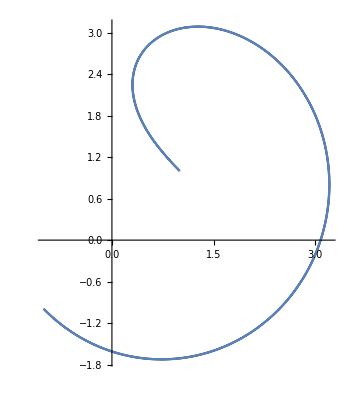

```mathematica
ParametricPlot[
{Cos[ⅇ^(-x^2/2) π]-ⅇ^(-x^2/2) π x^2 Cos[ⅇ^(-x^2/2) π]+Sin[ⅇ^(-x^2/2) π]+ⅇ^(-x^2/2) π x^2 Sin[ⅇ^(-x^2/2) π],Cos[ⅇ^(-x^2/2) π]+ⅇ^(-x^2/2) π x^2 Cos[ⅇ^(-x^2/2) π]-Sin[ⅇ^(-x^2/2) π]+ⅇ^(-x^2/2) π x^2 Sin[ⅇ^(-x^2/2) π]}
,{x,-5,5}]
```

```mathematica
{x,x}.RotationMatrix[θ ⅇ^(-x^2/2)]
```

{x Cos[ⅇ^(-x^2/2) θ]+x Sin[ⅇ^(-x^2/2) θ],x Cos[ⅇ^(-x^2/2) θ]-x Sin[ⅇ^(-x^2/2) θ]}

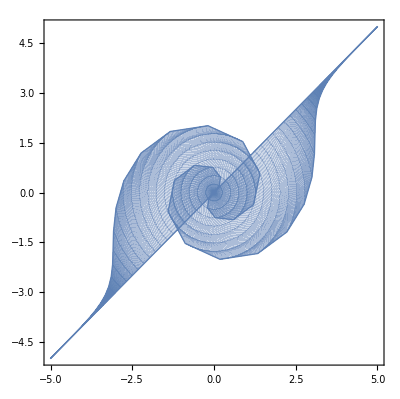

```mathematica
ParametricPlot[
{x Cos[ⅇ^(-x^2/2) θ]+x Sin[ⅇ^(-x^2/2) θ],x Cos[ⅇ^(-x^2/2) θ]-x Sin[ⅇ^(-x^2/2) θ]}
,{θ,0,2π},{x,-5,5}]
```

```mathematica
ParametricPlot[
{x Cos[ⅇ^(-x^2/2) θ]+x Sin[ⅇ^(-x^2/2) θ],x Cos[ⅇ^(-x^2/2) θ]-x Sin[ⅇ^(-x^2/2) θ]}
,{θ,0,2π},{x,-5,5}]
```

-Graphics-

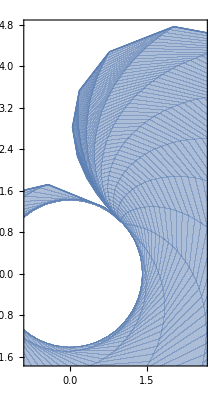

```mathematica
ParametricPlot[
{Cos[ⅇ^(-x^2/2) θ]-ⅇ^(-x^2/2) x^2 θ Cos[ⅇ^(-x^2/2) θ]+Sin[ⅇ^(-x^2/2) θ]+ⅇ^(-x^2/2) x^2 θ Sin[ⅇ^(-x^2/2) θ],Cos[ⅇ^(-x^2/2) θ]+ⅇ^(-x^2/2) x^2 θ Cos[ⅇ^(-x^2/2) θ]-Sin[ⅇ^(-x^2/2) θ]+ⅇ^(-x^2/2) x^2 θ Sin[ⅇ^(-x^2/2) θ]}
,{θ,0,2π},{x,-5,5}]
```

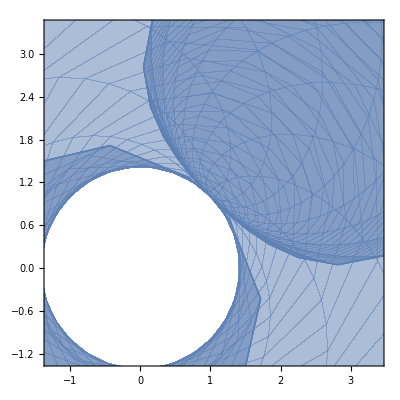

```mathematica
ParametricPlot[
{Cos[ⅇ^(-x^2/2) θ]-ⅇ^(-x^2/2) x^2 θ Cos[ⅇ^(-x^2/2) θ]+Sin[ⅇ^(-x^2/2) θ]+ⅇ^(-x^2/2) x^2 θ Sin[ⅇ^(-x^2/2) θ],Cos[ⅇ^(-x^2/2) θ]+ⅇ^(-x^2/2) x^2 θ Cos[ⅇ^(-x^2/2) θ]-Sin[ⅇ^(-x^2/2) θ]+ⅇ^(-x^2/2) x^2 θ Sin[ⅇ^(-x^2/2) θ]}
,{θ,-2π,2π},{x,-5,5}]
```

```mathematica
Laplacian[{x Cos[ⅇ^(-x^2/2) θ]+x Sin[ⅇ^(-x^2/2) θ],x Cos[ⅇ^(-x^2/2) θ]-x Sin[ⅇ^(-x^2/2) θ]},{x,θ}]
```

{-ⅇ^(-x^2) x Cos[ⅇ^(-x^2/2) θ]-3 ⅇ^(-x^2/2) x θ Cos[ⅇ^(-x^2/2) θ]+ⅇ^(-x^2/2) x^3 θ Cos[ⅇ^(-x^2/2) θ]-ⅇ^(-x^2) x^3 θ^2 Cos[ⅇ^(-x^2/2) θ]-ⅇ^(-x^2) x Sin[ⅇ^(-x^2/2) θ]+3 ⅇ^(-x^2/2) x θ Sin[ⅇ^(-x^2/2) θ]-ⅇ^(-x^2/2) x^3 θ Sin[ⅇ^(-x^2/2) θ]-ⅇ^(-x^2) x^3 θ^2 Sin[ⅇ^(-x^2/2) θ],-ⅇ^(-x^2) x Cos[ⅇ^(-x^2/2) θ]+3 ⅇ^(-x^2/2) x θ Cos[ⅇ^(-x^2/2) θ]-ⅇ^(-x^2/2) x^3 θ Cos[ⅇ^(-x^2/2) θ]-ⅇ^(-x^2) x^3 θ^2 Cos[ⅇ^(-x^2/2) θ]+ⅇ^(-x^2) x Sin[ⅇ^(-x^2/2) θ]+3 ⅇ^(-x^2/2) x θ Sin[ⅇ^(-x^2/2) θ]-ⅇ^(-x^2/2) x^3 θ Sin[ⅇ^(-x^2/2) θ]+ⅇ^(-x^2) x^3 θ^2 Sin[ⅇ^(-x^2/2) θ]}

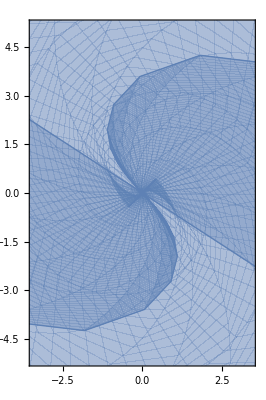

```mathematica
ParametricPlot[
{-ⅇ^(-x^2) x Cos[ⅇ^(-x^2/2) θ]-3 ⅇ^(-x^2/2) x θ Cos[ⅇ^(-x^2/2) θ]+ⅇ^(-x^2/2) x^3 θ Cos[ⅇ^(-x^2/2) θ]-ⅇ^(-x^2) x^3 θ^2 Cos[ⅇ^(-x^2/2) θ]-ⅇ^(-x^2) x Sin[ⅇ^(-x^2/2) θ]+3 ⅇ^(-x^2/2) x θ Sin[ⅇ^(-x^2/2) θ]-ⅇ^(-x^2/2) x^3 θ Sin[ⅇ^(-x^2/2) θ]-ⅇ^(-x^2) x^3 θ^2 Sin[ⅇ^(-x^2/2) θ],-ⅇ^(-x^2) x Cos[ⅇ^(-x^2/2) θ]+3 ⅇ^(-x^2/2) x θ Cos[ⅇ^(-x^2/2) θ]-ⅇ^(-x^2/2) x^3 θ Cos[ⅇ^(-x^2/2) θ]-ⅇ^(-x^2) x^3 θ^2 Cos[ⅇ^(-x^2/2) θ]+ⅇ^(-x^2) x Sin[ⅇ^(-x^2/2) θ]+3 ⅇ^(-x^2/2) x θ Sin[ⅇ^(-x^2/2) θ]-ⅇ^(-x^2/2) x^3 θ Sin[ⅇ^(-x^2/2) θ]+ⅇ^(-x^2) x^3 θ^2 Sin[ⅇ^(-x^2/2) θ]}
,{x,-5,5},{θ,0,2π}]
```

```mathematica
ParametricPlot3D[
{-ⅇ^(-x^2) x Cos[ⅇ^(-x^2/2) θ]-3 ⅇ^(-x^2/2) x θ Cos[ⅇ^(-x^2/2) θ]+ⅇ^(-x^2/2) x^3 θ Cos[ⅇ^(-x^2/2) θ]-ⅇ^(-x^2) x^3 θ^2 Cos[ⅇ^(-x^2/2) θ]-ⅇ^(-x^2) x Sin[ⅇ^(-x^2/2) θ]+3 ⅇ^(-x^2/2) x θ Sin[ⅇ^(-x^2/2) θ]-ⅇ^(-x^2/2) x^3 θ Sin[ⅇ^(-x^2/2) θ]-ⅇ^(-x^2) x^3 θ^2 Sin[ⅇ^(-x^2/2) θ],-ⅇ^(-x^2) x Cos[ⅇ^(-x^2/2) θ]+3 ⅇ^(-x^2/2) x θ Cos[ⅇ^(-x^2/2) θ]-ⅇ^(-x^2/2) x^3 θ Cos[ⅇ^(-x^2/2) θ]-ⅇ^(-x^2) x^3 θ^2 Cos[ⅇ^(-x^2/2) θ]+ⅇ^(-x^2) x Sin[ⅇ^(-x^2/2) θ]+3 ⅇ^(-x^2/2) x θ Sin[ⅇ^(-x^2/2) θ]-ⅇ^(-x^2/2) x^3 θ Sin[ⅇ^(-x^2/2) θ]+ⅇ^(-x^2) x^3 θ^2 Sin[ⅇ^(-x^2/2) θ],x}
,{x,-5,5},{θ,0,2π}]
```

-Graphics3D-

```mathematica
Manipulate[
ParametricPlot[
{x,x^2}.RotationMatrix[θ ⅇ^(-x^2/2)]
,{x,-5,5}]
,{θ,0,8π}]
```

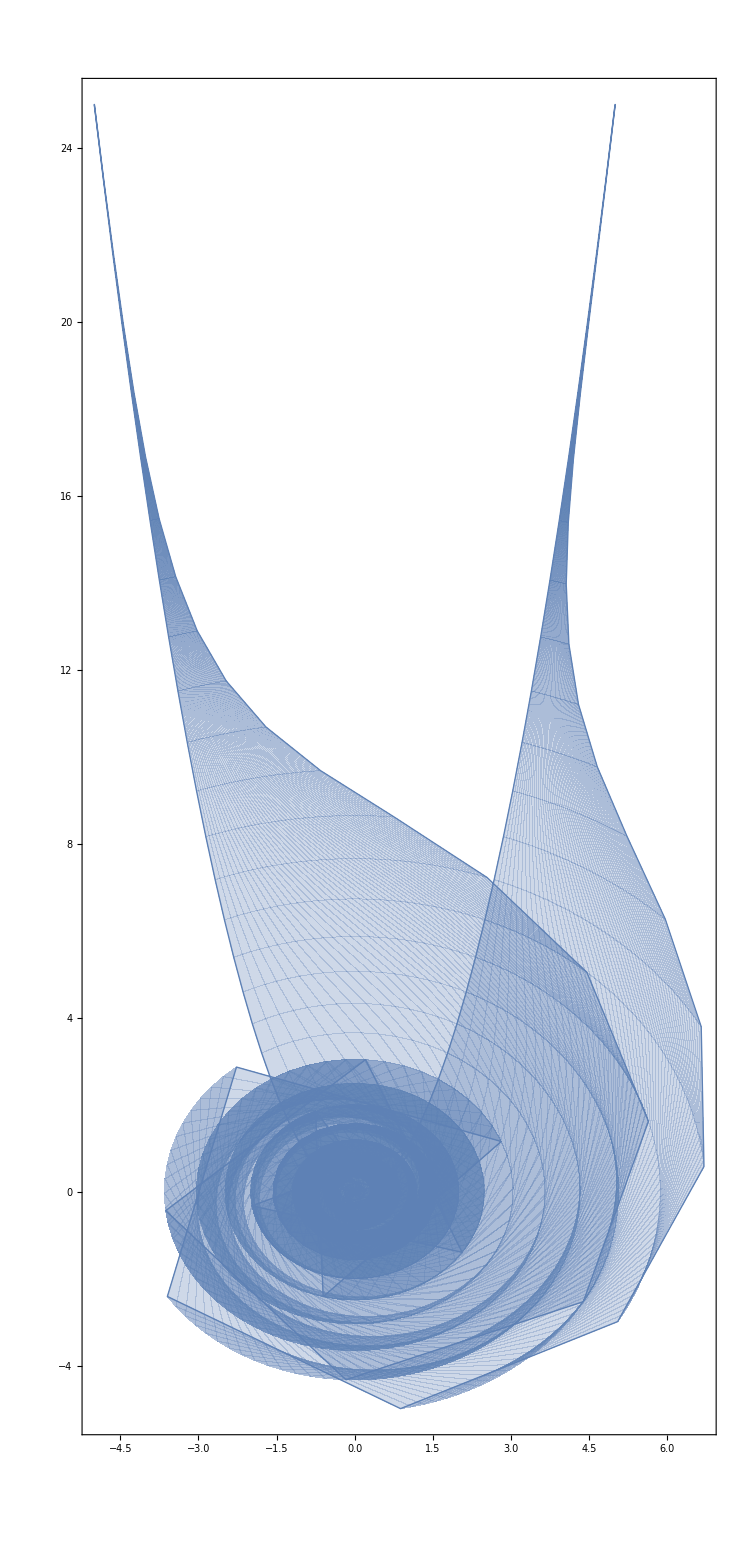

```mathematica
ParametricPlot[
{x,x^2}.RotationMatrix[θ ⅇ^(-x^2/2)]
,{x,-5,5},{θ,0,8π}]
```

```mathematica
Manipulate[
ParametricPlot[
{x,x^3}.RotationMatrix[θ ⅇ^(-x^2/2)]
,{x,-5,5}]
,{θ,0,8π}]
```

```mathematica
Manipulate[
ParametricPlot[
{x,Sin[x]}.RotationMatrix[θ ⅇ^(-x^2/2)]
,{x,-5,5}]
,{θ,0,8π}]
```

```mathematica
Manipulate[
ParametricPlot[
{x,ⅇ^(-x^2/2)}.RotationMatrix[θ ⅇ^(-x^2/2)]
,{x,-5,5}]
,{θ,0,8π}]
```

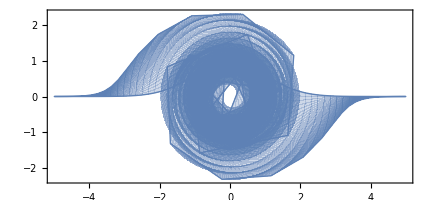

```mathematica
ParametricPlot[
{x,ⅇ^(-x^2/2)}.RotationMatrix[θ ⅇ^(-x^2/2)]
,{x,-5,5},{θ,0,8π}]
```

```mathematica
Manipulate[
ParametricPlot[
{x,x/θ}.RotationMatrix[θ ⅇ^(-x^2/2)]
,{x,-5,5}]
,{θ,0,8π}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
Manipulate[
ParametricPlot[
{x,x}.(RotationMatrix[θ ⅇ^(-x^2/2)]/θ)
,{x,-5,5}]
,{θ,0,8π}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
Manipulate[
ParametricPlot[
{x,x}.(RotationMatrix[θ ⅇ^(-x^2/2)]/θ)
,{x,-5,5}
,PlotRange->{{-2,2},{-2,2}}]
,{θ,0,8π}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
Manipulate[
ParametricPlot[
{x,x}.(RotationMatrix[θ ⅇ^(-x^2/2)]/θ)
,{x,-5,5}
,PlotRange->{{-5,5},{-5,5}}]
,{θ,0,8π}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
Manipulate[
ParametricPlot[
{x,x}.(RotationMatrix[θ ⅇ^(-x^2/2)]/θ)
,{x,-θ,θ}
,PlotRange->{{-5,5},{-5,5}}]
,{θ,0,8π}]
```

ParametricPlot::plld: Endpoints for x in {x,-FE`θ$$157,FE`θ$$157} must have distinct machine-precision numerical values.

General::stop: Further output of ParametricPlot::plld will be suppressed during this calculation.

```mathematica
Manipulate[
ParametricPlot[
{x,x}.(RotationMatrix[θ ⅇ^(-x^2/2)]/θ)
,{x,-10θ,10θ}
,PlotRange->{{-5,5},{-5,5}}]
,{θ,0,8π}]
```

ParametricPlot::plld: Endpoints for x in {x,-10 FE`θ$$161,10 FE`θ$$161} must have distinct machine-precision numerical values.

General::stop: Further output of ParametricPlot::plld will be suppressed during this calculation.

ParametricPlot::plld: Endpoints for x in {x,-10 FE`θ$$161,10 FE`θ$$161} must have distinct machine-precision numerical values.

General::stop: Further output of ParametricPlot::plld will be suppressed during this calculation.

```mathematica
Manipulate[
ParametricPlot[
{x,x}.(RotationMatrix[θ ⅇ^(-x^2/2)]/θ)
,{x,-10θ,10θ}
,PlotRange->{{-5,5},{-5,5}}]
,{θ,0.01,8π}]
```

General::munfl: Exp[-5899.78] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-10158.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-19663.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-27022.5] is too small to represent as a normalized machine number; precision may be lost.

```mathematica
Manipulate[
ParametricPlot[
{x,x}.(RotationMatrix[θ ⅇ^(-x^2/2)]/(√θ))
,{x,-10θ,10θ}
,PlotRange->{{-5,5},{-5,5}}]
,{θ,0.01,8π}]
```

General::munfl: Exp[-1004.27] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1748.53] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2904.65] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5603.43] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7996.35] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-27022.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-20013.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-15479.6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-12900.6] is too small to represent as a normalized machine number; precision may be lost.

```mathematica
Exp[-12900.63863308432]
```

General::munfl: Exp[-12900.6] is too small to represent as a normalized machine number; precision may be lost.

0.

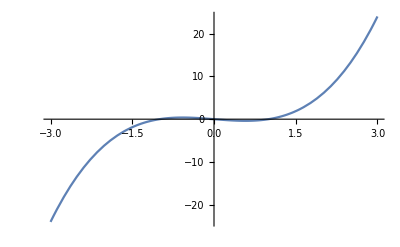

```mathematica
Plot[x^3-x,{x,-3,3}]
```

```mathematica
Sign'[x]=0
```

0

```mathematica
Sign'[3]
```

Sign'[3]

```mathematica
Map[Function[x,#]&,{x^3,x}]
```

{Function[x,x^3],Function[x,x]}

```mathematica
Map[(#''[x])/(√(1+#'[x]))^3&,{Function[x,x^3],Function[x,x]}]
```

{(6 x)/((1+3 x^2)^(3/2)),0}

```mathematica
Map[(#''[x])/(√(1+#'[x]))^3&,{Function[x,x^4],Function[x,x^3],Function[x,x^2],Function[x,x]}]
```

{(12 x^2)/((1+4 x^3)^(3/2)),(6 x)/((1+3 x^2)^(3/2)),2/(1+2 x)^(3/2),0}

```mathematica
FullSimplify[{(12 x^2)/((1+4 x^3)^(3/2)),(6 x)/((1+3 x^2)^(3/2)),2/(1+2 x)^(3/2),0},x∈Reals]
```

{(12 x^2)/((1+4 x^3)^(3/2)),(6 x)/((1+3 x^2)^(3/2)),2/(1+2 x)^(3/2),0}

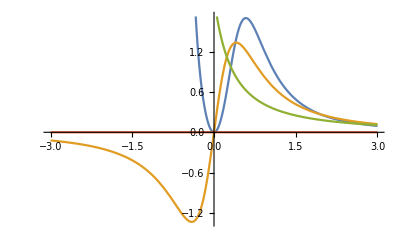

```mathematica
Plot[{(12 x^2)/((1+4 x^3)^(3/2)),(6 x)/((1+3 x^2)^(3/2)),2/(1+2 x)^(3/2),0},{x,-3,3}]
```

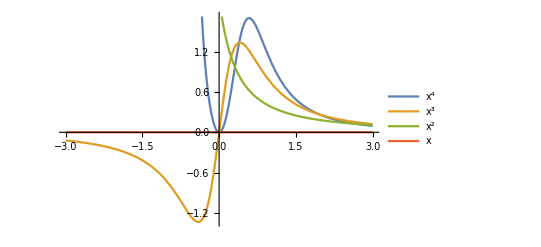

```mathematica
Plot[{(12 x^2)/((1+4 x^3)^(3/2)),(6 x)/((1+3 x^2)^(3/2)),2/(1+2 x)^(3/2),0},{x,-3,3},PlotLegends->{x^4,x^3,x^2,x}]
```

```mathematica
Abs[{(12 x^2)/((1+4 x^3)^(3/2)),(6 x)/((1+3 x^2)^(3/2)),2/(1+2 x)^(3/2),0}]
```

{12 Abs[x^2/((1+4 x^3)^(3/2))],6 Abs[x/((1+3 x^2)^(3/2))],2/Abs[1+2 x]^(3/2),0}

```mathematica
FullSimplify[{12 Abs[x^2/((1+4 x^3)^(3/2))],6 Abs[x/((1+3 x^2)^(3/2))],2/Abs[1+2 x]^(3/2),0}/(Total@{12 Abs[x^2/((1+4 x^3)^(3/2))],6 Abs[x/((1+3 x^2)^(3/2))],2/Abs[1+2 x]^(3/2),0}),x∈Reals]
```

{(6 x^2)/(((3 Abs[x])/((1+3 x^2)^(3/2))+1/Abs[1+2 x]^(3/2)+(6 x^2)/(Abs[1+4 x^3]^(3/2))) Abs[1+4 x^3]^(3/2)),(3 Abs[x])/((1+3 x^2)^(3/2) ((3 Abs[x])/((1+3 x^2)^(3/2))+1/Abs[1+2 x]^(3/2)+(6 x^2)/(Abs[1+4 x^3]^(3/2)))),1/(1+(3 Abs[x] Abs[1+2 x]^(3/2))/((1+3 x^2)^(3/2))+6 x^2 Abs[(1+2 x)/(1+4 x^3)]^(3/2)),0}

Power::infy: Infinite expression 1/0. encountered.

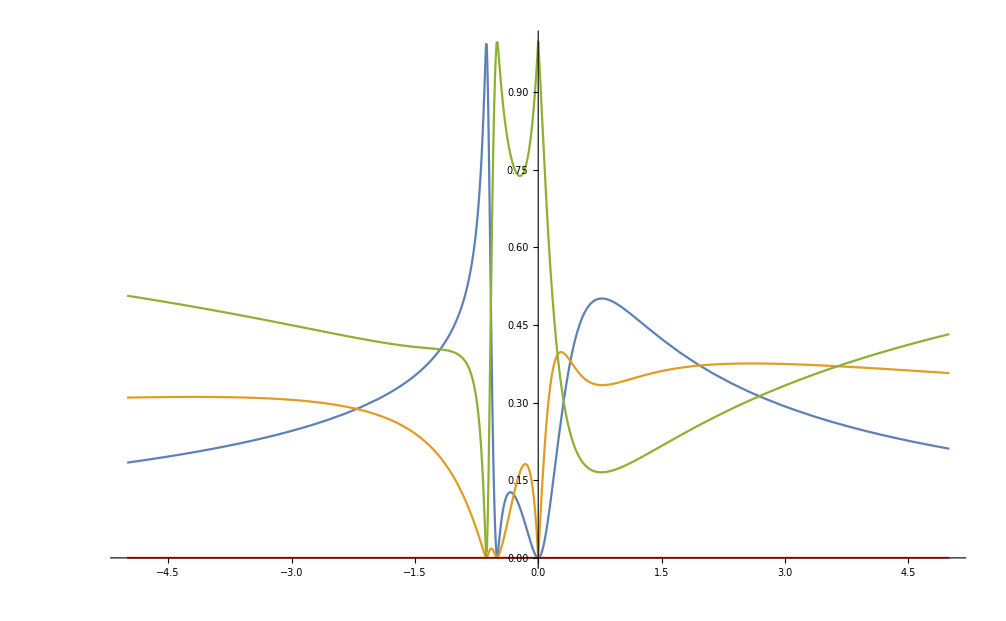

```mathematica
Plot[{(6 x^2)/(((3 Abs[x])/((1+3 x^2)^(3/2))+1/Abs[1+2 x]^(3/2)+(6 x^2)/(Abs[1+4 x^3]^(3/2))) Abs[1+4 x^3]^(3/2)),(3 Abs[x])/((1+3 x^2)^(3/2) ((3 Abs[x])/((1+3 x^2)^(3/2))+1/Abs[1+2 x]^(3/2)+(6 x^2)/(Abs[1+4 x^3]^(3/2)))),1/(1+(3 Abs[x] Abs[1+2 x]^(3/2))/((1+3 x^2)^(3/2))+6 x^2 Abs[(1+2 x)/(1+4 x^3)]^(3/2)),0},{x,-5,5}]
```

```mathematica
Total@{(6 x^2)/(((3 Abs[x])/((1+3 x^2)^(3/2))+1/Abs[1+2 x]^(3/2)+(6 x^2)/(Abs[1+4 x^3]^(3/2))) Abs[1+4 x^3]^(3/2)),(3 Abs[x])/((1+3 x^2)^(3/2) ((3 Abs[x])/((1+3 x^2)^(3/2))+1/Abs[1+2 x]^(3/2)+(6 x^2)/(Abs[1+4 x^3]^(3/2)))),1/(1+(3 Abs[x] Abs[1+2 x]^(3/2))/((1+3 x^2)^(3/2))+6 x^2 Abs[(1+2 x)/(1+4 x^3)]^(3/2)),0}==1
```

1/(1+(3 Abs[x] Abs[1+2 x]^(3/2))/((1+3 x^2)^(3/2))+6 x^2 Abs[(1+2 x)/(1+4 x^3)]^(3/2))+(3 Abs[x])/((1+3 x^2)^(3/2) ((3 Abs[x])/((1+3 x^2)^(3/2))+1/Abs[1+2 x]^(3/2)+(6 x^2)/(Abs[1+4 x^3]^(3/2))))+(6 x^2)/(((3 Abs[x])/((1+3 x^2)^(3/2))+1/Abs[1+2 x]^(3/2)+(6 x^2)/(Abs[1+4 x^3]^(3/2))) Abs[1+4 x^3]^(3/2))==1

```mathematica
Reduce[%53]
```

$Aborted

```mathematica
FullSimplify[
1/(1+(3 Abs[x] Abs[1+2 x]^(3/2))/((1+3 x^2)^(3/2))+6 x^2 Abs[(1+2 x)/(1+4 x^3)]^(3/2))+(3 Abs[x])/((1+3 x^2)^(3/2) ((3 Abs[x])/((1+3 x^2)^(3/2))+1/Abs[1+2 x]^(3/2)+(6 x^2)/(Abs[1+4 x^3]^(3/2))))+(6 x^2)/(((3 Abs[x])/((1+3 x^2)^(3/2))+1/Abs[1+2 x]^(3/2)+(6 x^2)/(Abs[1+4 x^3]^(3/2))) Abs[1+4 x^3]^(3/2))==1
,x∈Reals]
```

True

```mathematica
Simplify[
1/(1+(3 Abs[x] Abs[1+2 x]^(3/2))/((1+3 x^2)^(3/2))+6 x^2 Abs[(1+2 x)/(1+4 x^3)]^(3/2))+(3 Abs[x])/((1+3 x^2)^(3/2) ((3 Abs[x])/((1+3 x^2)^(3/2))+1/Abs[1+2 x]^(3/2)+(6 x^2)/(Abs[1+4 x^3]^(3/2))))+(6 x^2)/(((3 Abs[x])/((1+3 x^2)^(3/2))+1/Abs[1+2 x]^(3/2)+(6 x^2)/(Abs[1+4 x^3]^(3/2))) Abs[1+4 x^3]^(3/2))==1
]
```

(x (1+3 x^2) (Abs[1+2 x]^(3/2)-Abs[(1+2 x)/(1+4 x^3)]^(3/2) Abs[1+4 x^3]^(3/2)))/((3 Abs[x] Abs[1+2 x]^(3/2)+(1+3 x^2)^(3/2) (1+6 x^2 Abs[(1+2 x)/(1+4 x^3)]^(3/2))) ((1+3 x^2)^(3/2) Abs[1+4 x^3]^(3/2)+3 Abs[1+2 x]^(3/2) (2 x^2 (1+3 x^2)^(3/2)+Abs[x] Abs[1+4 x^3]^(3/2))))==0

```mathematica
x (1+3 x^2) (Abs[1+2 x]^(3/2)-Abs[(1+2 x)/(1+4 x^3)]^(3/2) Abs[1+4 x^3]^(3/2))==0
```

x (1+3 x^2) (Abs[1+2 x]^(3/2)-Abs[(1+2 x)/(1+4 x^3)]^(3/2) Abs[1+4 x^3]^(3/2))==0

```mathematica
Reduce[x (1+3 x^2) (Abs[1+2 x]^(3/2)-Abs[(1+2 x)/(1+4 x^3)]^(3/2) Abs[1+4 x^3]^(3/2))==0]
```

True

Power::infy: Infinite expression 1/0. encountered.

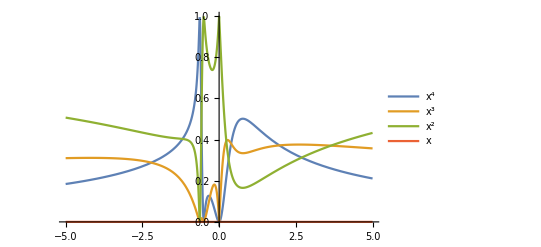

```mathematica
Plot[{(6 x^2)/(((3 Abs[x])/((1+3 x^2)^(3/2))+1/Abs[1+2 x]^(3/2)+(6 x^2)/(Abs[1+4 x^3]^(3/2))) Abs[1+4 x^3]^(3/2)),(3 Abs[x])/((1+3 x^2)^(3/2) ((3 Abs[x])/((1+3 x^2)^(3/2))+1/Abs[1+2 x]^(3/2)+(6 x^2)/(Abs[1+4 x^3]^(3/2)))),1/(1+(3 Abs[x] Abs[1+2 x]^(3/2))/((1+3 x^2)^(3/2))+6 x^2 Abs[(1+2 x)/(1+4 x^3)]^(3/2)),0},{x,-5,5}
,PlotLegends->{x^4,x^3,x^2,x}]
```

```mathematica
Manipulate[
NIntegrate[1/(1+(3 Abs[x] Abs[1+2 x]^(3/2))/((1+3 x^2)^(3/2))+6 x^2 Abs[(1+2 x)/(1+4 x^3)]^(3/2)),{x,-a,a}]
,{a,0.01,100}]
```

```mathematica
Manipulate[
NIntegrate[(3 Abs[x])/((1+3 x^2)^(3/2) ((3 Abs[x])/((1+3 x^2)^(3/2))+1/Abs[1+2 x]^(3/2)+(6 x^2)/(Abs[1+4 x^3]^(3/2)))),{x,-a,a}]
,{a,0.01,100}]
```

```mathematica
Manipulate[
NIntegrate[((3 Abs[x])/((1+3 x^2)^(3/2) ((3 Abs[x])/((1+3 x^2)^(3/2))+1/Abs[1+2 x]^(3/2)+(6 x^2)/(Abs[1+4 x^3]^(3/2)))))/a,{x,-a,a}]
,{a,0.01,100}]
```

```mathematica
Limit[
Integrate[((3 Abs[x])/((1+3 x^2)^(3/2) ((3 Abs[x])/((1+3 x^2)^(3/2))+1/Abs[1+2 x]^(3/2)+(6 x^2)/(Abs[1+4 x^3]^(3/2)))))/a,{x,-a,a}],a->∞]
```

$Aborted

```mathematica
Series[1/x,{x,0,10}]
```

1/x+O[x]^11

```mathematica
Normal[1/x+O[x]^11]
```

1/x

```mathematica
CoefficientList[1/x+O[x]^11,x]
```

CoefficientList::poly: 1/x is not a polynomial.

{1/x}

```mathematica
InverseSeries[1/x+O[x]^11]
```

1/x+O[1/x]^13

```mathematica
PadeApproximant[Normal[1/x+O[x]^11],{x,0,5}]
```

1/x

```mathematica
CoefficientList[1/x+O[x]^11,x]
```

CoefficientList::poly: 1/x is not a polynomial.

{1/x}

```mathematica
Sum[a^n Cos[b^n π x],{x,0,n}]
```

1/2 a^n (1-Cos[b^n (1+n) π]+Cot[(b^n π)/2] Sin[b^n (1+n) π])

```mathematica
Sum[a^n Cos[b^n π x],{x,0,m}]
```

1/2 a^n (1-Cos[b^n (1+m) π]+Cot[(b^n π)/2] Sin[b^n (1+m) π])